```mathematica
c=2;
Ln=4;
```

Probability l<c

```mathematica
P1[l_,p_]:=p^l*(1-p)
```

Probability c<=l<L

```mathematica
P2[l_,p_]:=p^l*(1-p)/2
```

Probability l=L

```mathematica
P3[L_,p_]:=p^L/2
```

```mathematica
S1[c_,p_]:=Sum[P1[l,p]*Log[P1[l,p]],{l,0,c-1}]
```

```mathematica
S2[L_,c_,p_]:=Sum[P2[l,p]*Log[P2[l,p]],{l,c,L-1}]
En2[L_,c_,p_]:= -(S1[c,p]+2*S2[L,c,p]+2*P3[L,p]*Log[P3[L,p]])
```

```mathematica
S4[L_,p_]:=Sum[P1[l,p]*Log[P1[l,p]],{l,0,L-1}]
```

```mathematica
Em2[L_,p_]:=-(S4[L,p]+p^L*Log[p^L])
```

Adjusted rates

```mathematica
h[τ_]:=1/(1+1/τ)
```

p^L Log[p^L/2]

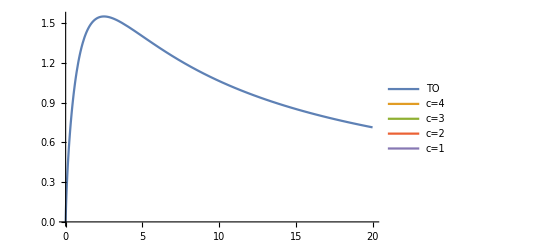

```mathematica
T1=Evaluate@Table[En[4,c,h[τ]],{c,1,4}];2*P3[L,p]*Log[P3[L,p]]
Plot[{Em2[4,h[τ]],T1},{τ,0,20},PlotLegends->{"TO","c=4","c=3","c=2","c=1"}]
```

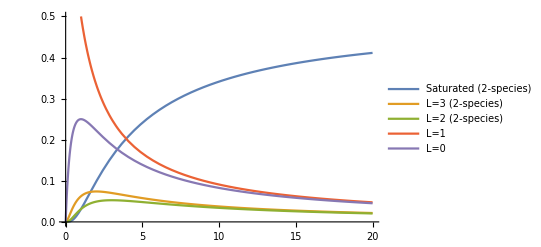

```mathematica
T4=Evaluate@Table[P1[l,h[τ]],{l,0,c-1}];
T5=Evaluate@Table[P2[l,h[τ]],{l,c,Ln-1}];
Plot[{P3[Ln,h[τ]],T5,T4},{τ,0,20},PlotRange->{0,0.5},PlotLegends->{"Saturated (2-species)","L=3 (2-species)","L=2 (2-species)","L=1","L=0"}]
```

```mathematica
NT4=Length[T4];
NT5=Length[T5];
```

```mathematica
TT42=Evaluate@Table[Sum[T4[[{i}]],{i,1,j}],{j,1,NT4}];
TT52=Evaluate@Table[TT42[[NT4]]+Sum[T5[[{i}]],{i,1,j}],{j,1,NT5}];
TT53=Evaluate@Table[TT52[[NT5]]+Sum[T5[[{i}]],{i,1,j}],{j,1,NT5}];
CU1[L_,τ_]:=TT53[[NT5]]+P3[L,h[τ]];
CU2[L_,τ_]:=CU1[L,τ]+P3[L,h[τ]];
```

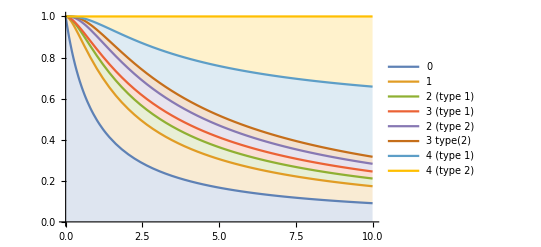

```mathematica
Plot[{TT42,TT52,TT53,CU1[Ln,τ],CU2[Ln,τ]},{τ,0,10},PlotLegends->{"0","1","2 (type 1)","3 (type 1)","2 (type 2)","3 type(2)","4 (type 1)","4 (type 2)"}, Filling->{1->Axis,2->{1},3->{2},4->{3},5->{4},6->{5},7->{6},8->{7}}]
```

```mathematica
T43=Evaluate@Table[τ/.Solve[P1[i,h[τ]]==1/20&& τ>0],{i,0,c-1}]
```

{{19},{9-4 √5,9+4 √5}}

```mathematica
T53=Evaluate@Table[τ/.Solve[P2[i,h[τ]]==1/20&& τ>0],{i,c,Ln-1}]
```

{{Root[1+3 #1-7 #1^2+#1^3&,2],Root[1+3 #1-7 #1^2+#1^3&,3]},{Root[1+4 #1+6 #1^2-6 #1^3+#1^4&,1],Root[1+4 #1+6 #1^2-6 #1^3+#1^4&,2]}}

```mathematica
L2=τ/.Solve[P3[Ln,h[τ]]==1/20&&τ>0]
```

{Root[-1-4 #1-6 #1^2-4 #1^3+9 #1^4&,2]}

```mathematica
a[x_]:=0.2/;x<19
b[x_]:=0.4/;T43[[2]][[1]]<x<T43[[2]][[2]]
d[x_]:=0.6/;T53[[1]][[1]]<x<T53[[1]][[2]]
e[x_]:=0.8/;T53[[2]][[1]]<x<T53[[2]][[2]]
f[x_]:=1/;L2[[1]]<x<22
```

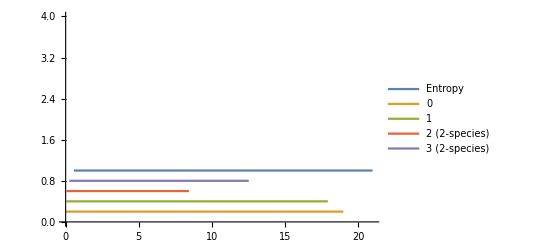

```mathematica
Plot[{f[x],a[x],b[x], d[x], e[x]},{x,0,21}, PlotRange->{0,4}, PlotLegends->{"Entropy","0","1","2 (2-species)","3 (2-species)","4 (2-species)"}]
```